# Field quantization

Install and load the Quantum Framework paclet:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
```

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

## Quantization of a single mode field

Let’s start with the simple case of a 1D cavity  along the z axis with perfectly conducting walls at z = 0 and z = L. Assuming the electric field is polarized in the x direction E(r,t) =  e_x E_x (z,t) where e_x is a unit vector along x, we also assume there are no sources of radiation (charges, currents, etc).

Maxwell equations without sources in SI units:




A single mode field  that satisfy the equations with the boundary conditions:

Where ω is the mode frequency , k is the wave number and V is the effective cavity volume . The boundary conditions allow  ω_m = c (m π / L), m = 1,2,...

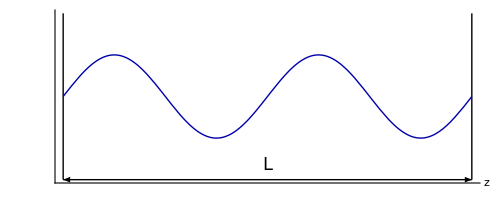

```mathematica
Show[{Graphics[{Line[{{0,-2},{0,2}}],Line[{{4Pi,-2},{4Pi,2}}],Arrowheads[{-.05,.05}],Arrow[{{0,-2},{4Pi,-2}}],Text[Style["L",18],{2Pi,-1.65}]}],Plot[Sin[x],{x,0,4Pi},PlotStyle->Directive[Darker[Blue],Thick]]},Axes->True,Ticks->None, AxesLabel->{"z",""}]
```

In a similar way the magnetic field in the cavity is B(r , t) = e_y B_y(z, t) where:
 
q(t)  is a time dependent function that represents canonical position and  q̇(t) = p(t) represents canonical momentum with unit mass.
The energy of the field that coincides with  Hamiltonian H is
 
It can be shown  that is equivalent to an harmonic oscillator of unit mass, where p and q  are canonical momentum and position up to scaling factors

Quantizing the harmonic oscillator of unit mass promotes the canonical variables p and q to operators p̂ and q̂ that satisfy the commutation relation

So the Hamiltonian becomes:

It is standard to introduce  non Hermitian(non observable) operators â and (â)^† which have more significance than just for sake of algebraic manipulation


Electric and magnetic field become


Where  ℰ_0 = (ℏ ω / ϵ_0 V)^(1/2) and ℬ_0 = (μ_0/k)(ϵ_0 ℏ ω^3/V)^(1/2) can be interpreted as electric and magnetic fields per photon. However, this is not really correct , because we will show a quantum state with a definite number of photons has expectation value of zero of these operators.

The â and (â)^† operators follow the commutation relation  and as a result ,   is called the number operator . Considering  |n⟩  an energy eigenstate then the eigenvalue equation  is
 
 Multiplying by (â)^†

## Definitions

Creation and annihilation operator of size n:

```mathematica
creationAnnihilation[n_]:=Module[{ca,aa},
aa=QuantumOperator[Table[If[i==j+1,Sqrt[i-1],0],{i,1,n},{j,1,n}],n];
ca=aa["Dagger"];
{ca,aa}]
```

Particular nth Fock state in a basis of size d:

```mathematica
fockN[n_,d_]:= QuantumState[SparseArray[{n+1 -> 1}, d], d]
```

## Basic properties of creation and annihilation operators

We can specify the size of  the Fock space

```mathematica
size = 11;
```

```mathematica
{a,a†} = creationAnnihilation[size];
```

```mathematica
fockBasis = a["OutputBasis"]
```

<|0→{1,0,0,0,0,0,0,0,0,0,0},1→{0,1,0,0,0,0,0,0,0,0,0},2→{0,0,1,0,0,0,0,0,0,0,0},3→{0,0,0,1,0,0,0,0,0,0,0},4→{0,0,0,0,1,0,0,0,0,0,0},5→{0,0,0,0,0,1,0,0,0,0,0},6→{0,0,0,0,0,0,1,0,0,0,0},7→{0,0,0,0,0,0,0,1,0,0,0},8→{0,0,0,0,0,0,0,0,1,0,0},9→{0,0,0,0,0,0,0,0,0,1,0},10→{0,0,0,0,0,0,0,0,0,0,1}|>

Creation  and  annihilation are  non Hermitian operators with commutator

```mathematica
a @ fockN[5,size]
```

√5 4

```mathematica
a† @ fockN[5,size]
```

√6 6

Nested application of the annihilation  operator eventually makes any number state goes to the vacuum , and one more application returns the scalar zero:

```mathematica
NestList[a,fockN[size-1,size],size]
```

{10,√10 9,3 √108,12 √57,12 √356,12 √2105,60 √424,120 √423,360 √142,720 √71,720 √70,0}

It is possible to  build  nth Fock state from vacuum |n⟩ = ((a^†)^n)/(√(n!))|0⟩

```mathematica
Nest[a†,QuantumState["0",size],5]/√Factorial[5]
```

5

Photon number operator (observable) :

```mathematica
numberOp =a†@a
```

11+222+333+444+555+666+777+888+999+101010

```mathematica
st = QuantumState[1/Sqrt[2]SparseArray[{3->1,8->1},10],fockBasis]
```

1/(√2)2+1/(√2)7

Mean number of photons using QuantumMeasurementOperator and alternative approach:

```mathematica
(QuantumMeasurementOperator[numberOp]@st)["Mean"]//AbsoluteTiming
```

{0.30062,9/2}

```mathematica
KeyValueMap[#1[[1]] #2 &, st["Probability"]]//Total //AbsoluteTiming
```

{0.0008396,9/2}

## Quantum fluctuations for a single mode field

The energy eigenstate |n⟩ has well defined energy but does not have a well defined electric field because
⟨ n |E_x( z,t)|n ⟩ =  ℰ_0 sin(k z)[ ⟨n|a|n⟩ + ⟨ n|a^†| n⟩ ] =  0

```mathematica
fieldOp = Subscript[ℰ, 0] Sin[k z](a+a†);
```

```mathematica
(#["Dagger"]@fieldOp @ #)["Scalar"]& /@ Table[fockN[n,size],{n,0,size-1}]
```

{0,0,0,0,0,0,0,0,0,0,0}

However, the electric field squared is not zero:
⟨ n |E_x^2( z,t)|n ⟩ =  (ℰ^2)_0 sin^2(k z)[ ⟨n|(a^†)^2 +a^2+a^†a + a a^†|n⟩] =  (ℰ^2)_0 sin^2(k z) ⟨n|(a^†)^2 +a^2+2 a^†a + 1|n⟩] = (ℰ^2)_0 sin^2(k z) (2  n + 1)

```mathematica
(#["Dagger"]@fieldOp@fieldOp @ #)["Scalar"]& /@ Table[fockN[n,size],{n,0,size-2}]
```

{Sin[k z]^2 ℰ_0^2,3 Sin[k z]^2 ℰ_0^2,5 Sin[k z]^2 ℰ_0^2,7 Sin[k z]^2 ℰ_0^2,9 Sin[k z]^2 ℰ_0^2,11 Sin[k z]^2 ℰ_0^2,13 Sin[k z]^2 ℰ_0^2,15 Sin[k z]^2 ℰ_0^2,17 Sin[k z]^2 ℰ_0^2,19 Sin[k z]^2 ℰ_0^2}

For an operator the variance is defined as and the standard deviation or uncertainty is the square root of the variance so for a number state we have :
ΔE_x = √(2 ℰ_0) sin(k z) √(n + 1/2)    even when n = 0 the mean field is zero  but has non zero uncertainty , this phenomenon is called vacuum fluctuations. So a state with definite number of photons has zero  average field . This is related to uncertainty principle because n̂ and OverHat[E_x] do not commute [n, E_x] = ℰ_0 sin(k z) (a^†-a), the operators are complementary

## Quadrature operators of a single mode field

We define helper functions for the commutator and operator variance:

```mathematica
commutator[a_QuantumOperator,b_QuantumOperator]:=a@b - b@a 
operatorVariance[state_QuantumState, op_QuantumOperator]:= (state["Dagger"]@ (op @ op)@ state)["Scalar"] - (state["Dagger"]@ op @ state)["Scalar"]^2
```

```mathematica
setFockSize[40]
```

```mathematica
X1 = 1/2(a+a["Dagger"]);
```

```mathematica
X2 = 1/(2I)(a-a["Dagger"]);
```

,   but there is an error in the last term because of truncation

```mathematica
commutator[X1,X2]["Matrix"]//Diagonal //Normal
```

{ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,-(39 ⅈ)/2}

For a fock state , the ground state |0⟩attains the minimum value  1/4

```mathematica
With[{fockstates = fockBasis["BasisStates"][[1;;10]]},Table[{operatorVariance[ fockstate,X1],operatorVariance[ fockstate,X2]},{fockstate,fockstates}]]
```

{{1/4,1/4},{3/4,3/4},{5/4,5/4},{7/4,7/4},{9/4,9/4},{11/4,11/4},{13/4,13/4},{15/4,15/4},{17/4,17/4},{19/4,19/4}}

## Thermal fields

Considering  a single mode field in thermal equilibrium in a cavity at temperature T. From statistical mechanics the probability distribution  P_n that the n-th level is excited is:

where k_B is the Boltzmann constant

Using  the Hamiltonian  a mixed state described by a thermal density operator is defined based on the energy probability distribution:

The denominator is the partition function

```mathematica
En = h ω (n + 1/2);
```

The partition function Z is obtained:

```mathematica
Z =Sum[Exp[-En/(kb T)],{n,0,∞}]
```

ⅇ^((h ω)/(2 kb T))/(-1+ⅇ^((h ω)/(kb T)))

The probability distribution of having a state that has n photons is:

The average photon number is :

```mathematica
Sum[n Exp[-En/(kb T)],{n,0,∞}]/Z
```

1/(-1+ⅇ^((h ω)/(kb T)))

ρ_Th can be written in terms of n^— as:

```mathematica
thermalState[nbar_, size_]:=QuantumOperator[DiagonalMatrix [1/(1+nbar) Table[(nbar/(1+nbar))^n,{n,0,size}]],size+1]["MatrixQuantumState"]
```

```mathematica
thermalState[2.,39];
```

```mathematica
% // Tr
```

1.

Thermal field photon distribution varying the n^— parameter of the thermal state density matrix:

```mathematica
Manipulate[thermalState[nmean,fockBasis["Dimension"]-1]["ProbabilityPlot",PlotRange->{{-1,11.5},{0,1}},PlotRangePadding->0.09],{{nmean,0.1,"n^—"},0.1,2.,0.1},SaveDefinitions->True]
```

## Vacuum fluctuations

We showed quantized radiation presents fluctuations and is of special interest the case of the vacuum. The zero point energy (ZPE) arises from the fact that [a,a^†] ≠ 0

## The quantum phase

## Exercises